```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
d1rhoV[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*((-(dmf2d1rho[h,ρ] nfd1xa[mf2[h,ρ],q,T,μ])/(2 √(q^2+mf2[h,ρ]))-(dmf2d1rho[h,ρ] nfd1xf[mf2[h,ρ],q,T,μ])/(2 √(q^2+mf2[h,ρ])))/(2 √(q^2+mf2[h,ρ]))-(dmf2d1rho[h,ρ] (-nfa[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],q,T,μ]))/(4 (q^2+mf2[h,ρ])^(3/2))),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10];
d2rhoV[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*(-(dmf2d1rho[h,ρ] (-(dmf2d1rho[h,ρ] nfd1xa[mf2[h,ρ],q,T,μ])/(2 √(q^2+mf2[h,ρ]))-(dmf2d1rho[h,ρ] nfd1xf[mf2[h,ρ],q,T,μ])/(2 √(q^2+mf2[h,ρ]))))/(2 (q^2+mf2[h,ρ])^(3/2))+1/(2 √(q^2+mf2[h,ρ]))((dmf2d1rho[h,ρ]^2 nfd1xa[mf2[h,ρ],q,T,μ])/(4 (mf2[h,ρ]+q^2)^(3/2))-(dmf2d2rho[h,ρ] nfd1xa[mf2[h,ρ],q,T,μ])/(2 √(q^2+mf2[h,ρ]))+(dmf2d1rho[h,ρ]^2 nfd1xf[mf2[h,ρ],q,T,μ])/(4 (mf2[h,ρ]+q^2)^(3/2))-(dmf2d2rho[h,ρ] nfd1xf[mf2[h,ρ],q,T,μ])/(2 √(q^2+mf2[h,ρ]))-(dmf2d1rho[h,ρ]^2 nfd2xa[mf2[h,ρ],q,T,μ])/(4 (q^2+mf2[h,ρ]))-(dmf2d1rho[h,ρ]^2 nfd2xf[mf2[h,ρ],q,T,μ])/(4 (q^2+mf2[h,ρ])))+1/2 ((3 dmf2d1rho[h,ρ]^2)/(4 (q^2+mf2[h,ρ])^(5/2))-dmf2d2rho[h,ρ]/(2 (q^2+mf2[h,ρ])^(3/2))) (-nfa[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],q,T,μ])),{q,0,50.,100.,200.,500.,1000.,5000.},WorkingPrecision->15,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10];
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ=75.8;
ν=-482.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=300;
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

# Mean-field effective potential

```mathematica
sigmadata=Import["./sigma0.dat"];
sigmadata2=Import["./sigma0p2.dat"];
mu=Table[i*5.,{i,1,80}];
mu2=Table[i,{i,290,310}];
```

```mathematica
Length[sigmadata]
```

80

```mathematica
Length[sigmadata2]
```

21

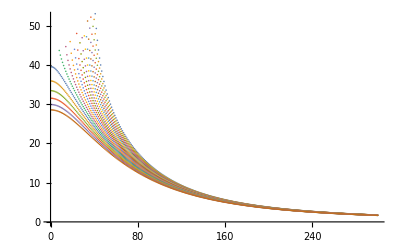

```mathematica
ListPlot[sigmadata2]
```

## effective potential

92.325526

135.695

480.438

300.058

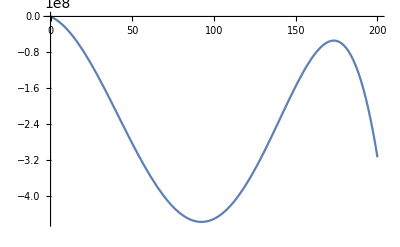

```mathematica
a=FindMinimum[{V[a1^2/2,h,1,0.,λ,ν,c]+Vvacuum[a1^2/2,h,M1],0<a1<195},{a1,90},WorkingPrecision->8][[2]][[1]][[2]]//Quiet

√Vd1rhovacuum[a^2/2,h,λ,ν,M1]
√(Vd1rhovacuum[a^2/2,h,λ,ν,M1]+2*a^2/2*Vd2rhovacuum[a^2/2,h,λ,ν,M1])
√mf2[h,a^2/2]
Plot[{V[a^2/2,h,1,0,λ,ν,c]+Vvacuum[a^2/2,h,M1]},{a,0,200},PlotRange->All]
```

```mathematica
d2rhoV[sigmadata[[1]]^2/2,h,1,0,λ,ν,c]
```

-2.09210910807785×10^-130

```mathematica
mpp1=ParallelTable[Table[√(Vd1rhovacuum[(sigmadata[[j]][[i]])^2/2,h,λ,ν,M1]+d1rhoV[(sigmadata[[j]][[i]])^2/2,h,i,mu[[j]],λ,ν,c]),{i,1,300}],{j,1,80}];
msp1=ParallelTable[Table[√((Vd1rhovacuum[(sigmadata[[j]][[i]])^2/2,h,λ,ν,M1]+d1rhoV[(sigmadata[[j]][[i]])^2/2,h,i,mu[[j]],λ,ν,c])+2*(sigmadata[[j]][[i]])^2/2*(Vd2rhovacuum[(sigmadata[[j]][[i]])^2/2,h,λ,ν,M1]+d2rhoV[(sigmadata[[j]][[i]])^2/2,h,N[i],mu[[j]],λ,ν,c])),{i,1,300}],{j,1,80}];
```

$Aborted

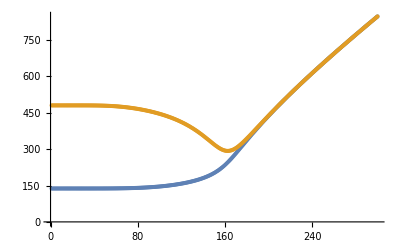

```mathematica
ListPlot[{mp,ms}]
```

```mathematica
Export["./mpion_T.dat",mp];
Export["./msigma_T.dat",ms];
```